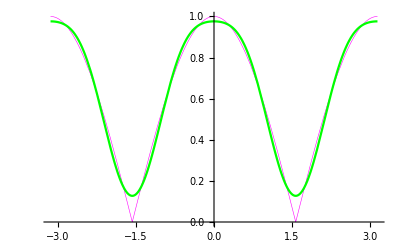

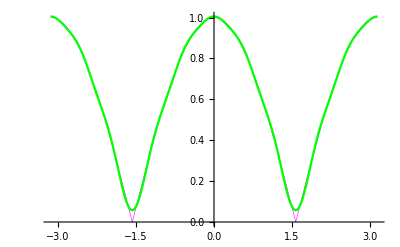

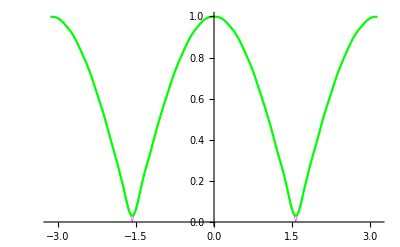

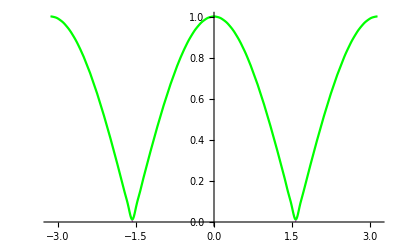

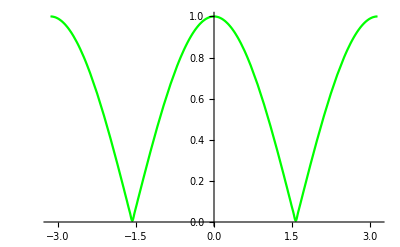

```mathematica
Clear[f,a,b,s];
f[x_] := Abs[Cos[x]];
fig[l_]:=Plot[Evaluate[f[x]],{x,-l,l},PlotStyle->{Thickness[0.001],RGBColor[1,0,1]},PlotRange->All]
a[k_,l_]:=(1/l)Integrate[f[t]Cos[(k Pi t)/l],{t,-l,l}];
b[k_,l_]:=(1/l)Integrate[f[t]Sin[(k Pi t)/l],{t,-l,l}];
s[n_,x_,l_]:= a[0,l]/2 + Sum[a[k,l]Cos[(k Pi x )/l] + b[k,l]Sin[(k Pi x)/ l],{k,1,n}];
nsumfig[n_,l_] := Plot[Evaluate[s[n,x,l]],{x,-l,l},PlotStyle->{Thickness[0.004],RGBColor[0,1,0]},PlotRange->All];
Show[fig[Pi],nsumfig[5,Pi]]
Show[fig[Pi],nsumfig[10,Pi]]
Show[fig[Pi],nsumfig[20,Pi]]
Show[fig[Pi],nsumfig[50,Pi]]

Show[fig[Pi],nsumfig[100,Pi]]
```

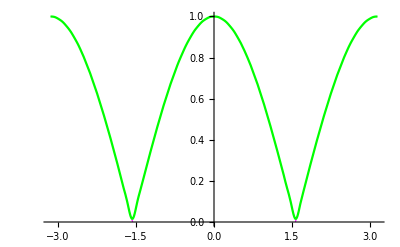

```mathematica
Show[fig[Pi],nsumfig[40,Pi]]
```

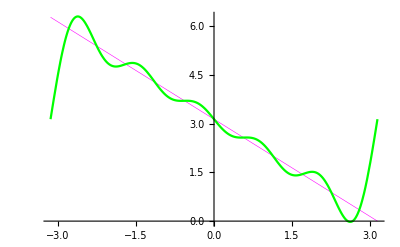

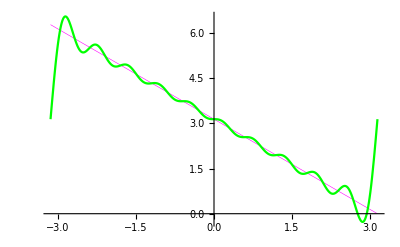

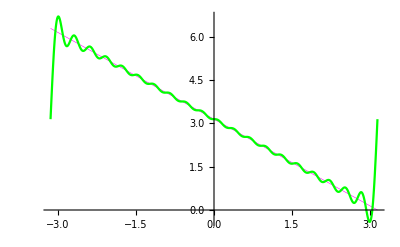

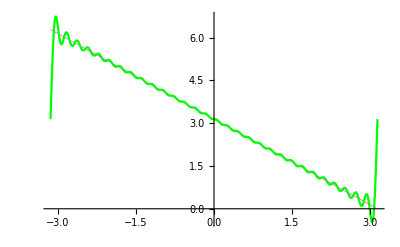

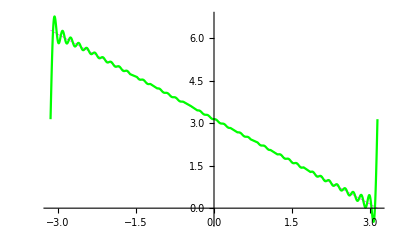

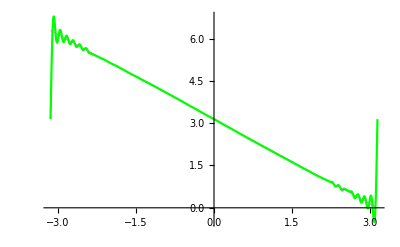

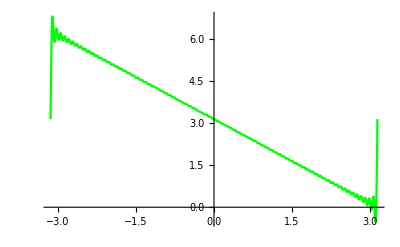

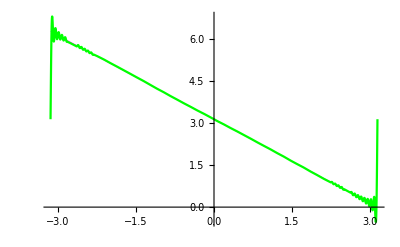

```mathematica
Clear[f]
f[x_]:= Pi -x;
Show[fig[Pi],nsumfig[5,Pi]]
Show[fig[Pi],nsumfig[10,Pi]]
Show[fig[Pi],nsumfig[20,Pi]]
Show[fig[Pi],nsumfig[30,Pi]]
Show[fig[Pi],nsumfig[40,Pi]]
Show[fig[Pi],nsumfig[50,Pi]]

Show[fig[Pi],nsumfig[80,Pi]]

Show[fig[Pi],nsumfig[100,Pi]]
```

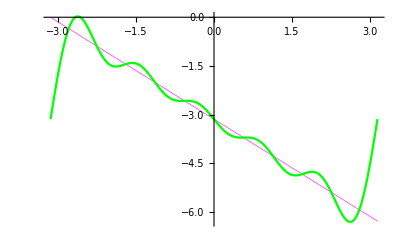

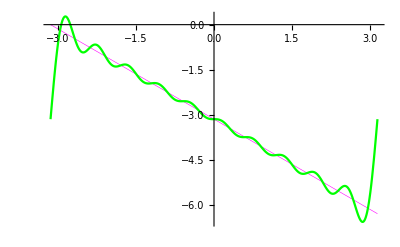

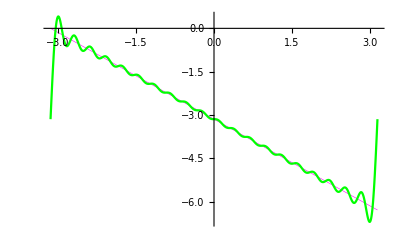

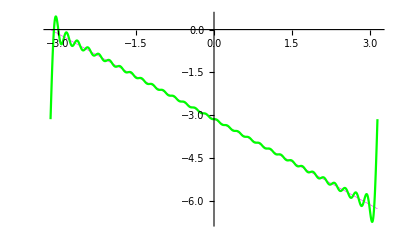

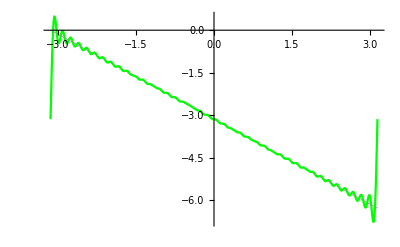

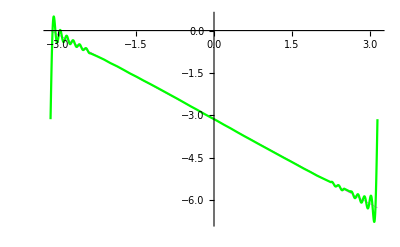

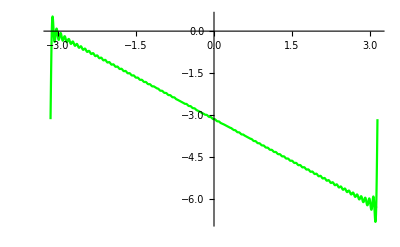

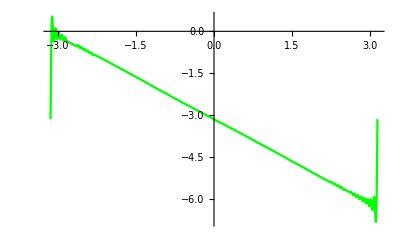

```mathematica
Clear[f]
f[x_]:= -Pi -x;
Show[fig[Pi],nsumfig[5,Pi]]
Show[fig[Pi],nsumfig[10,Pi]]
Show[fig[Pi],nsumfig[20,Pi]]
Show[fig[Pi],nsumfig[30,Pi]]
Show[fig[Pi],nsumfig[40,Pi]]
Show[fig[Pi],nsumfig[50,Pi]]
Show[fig[Pi],nsumfig[80,Pi]]
Show[fig[Pi],nsumfig[100,Pi]]
```